# Small V

## General definitions

### Base quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

ClearAll[gLL];
gLL=FullSimplify[Inverse[gUU]];
```

### ADM quantities

```mathematica
ClearAll[scoordsU];
scoordsU=coordsU[[2;;4]];

ClearAll[γLL,γUU];
γLL=gLL[[2;;4,2;;4]];
γUU=FullSimplify[Inverse[γLL]];

ClearAll[lapse];
lapse=Simplify[Sqrt[-1/gUU[[1,1]]],α[t,x,y,z]>=0];

ClearAll[βU,βL];
βU=gUU[[1,2;;4]]α[t,x,y,z]^2;
βL=gLL[[1,2;;4]];

ClearAll[KLL];
KLL=Table[
1/(2lapse)(D[βL[[j]],scoordsU[[i]]]+D[βL[[i]],scoordsU[[j]]]),
{i,1,3},
{j,1,3}
]//FullSimplify;

ClearAll[nU,nL];
nU=Join[{1/lapse},-βU/lapse];
nL=FullSimplify[Table[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

### 4-Christoffel symbols

```mathematica
ClearAll[Γ];
Γ=Table[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;
```

### Geodesic equation checker

Compute the geodesic equations from a 4-velocity vector

```mathematica
ClearAll[geodesicEquations]
geodesicEquations[velU_,velL_]:=FullSimplify[
Table[
Sum[velU[[a]]D[velL[[b]],coordsU[[a]]],{a,1,4}]
-Sum[velU[[a]]Γ[[i,a,b]]velL[[i]],{i,1,4},{a,1,4}],
{b,1,4}
]
];
```

### Vincent geodesic equations

```mathematica
ClearAll[VU];
VU={velx,vely,velz};

ClearAll[dXudt];
dXudt=FullSimplify[
Table[
lapse*VU[[i]]-βU[[i]],
{i,1,3}
]
];

ClearAll[dVUdt];
dVUdt=FullSimplify[
Table[
Sum[lapse*VU[[j]]VU[[i]]D[Log[lapse],scoordsU[[j]]],{j,1,3}]
-Sum[lapse*VU[[j]]VU[[i]]KLL[[j,k]]VU[[k]],{j,1,3},{k,1,3}]
+2Sum[lapse*VU[[j]]γUU[[i,k]]KLL[[k,j]],{k,1,3},{j,1,3}]
-Sum[γUU[[i,j]]D[lapse,scoordsU[[j]]],{j,1,3}]
-Sum[VU[[j]]D[βU[[i]],scoordsU[[j]]],{j,1,3}]
,
{i,1,3}
]
];

ClearAll[dEdt];
dEdt=FullSimplify[
energy(Sum[lapse*KLL[[j,k]]VU[[j]]VU[[k]],{j,1,3},{k,1,3}]-Sum[VU[[j]]D[lapse,scoordsU[[j]]],{j,1,3}])
];
```

```mathematica
dVUdt
```

{velx^2 velz vx^(0,0,0,1)[t,x,y,z]+velx vely velz vy^(0,0,0,1)[t,x,y,z]+velx velz^2 vz^(0,0,0,1)[t,x,y,z]+velx velz α^(0,0,0,1)[t,x,y,z]+velx^2 vely vx^(0,0,1,0)[t,x,y,z]+velx vely^2 vy^(0,0,1,0)[t,x,y,z]+velx vely velz vz^(0,0,1,0)[t,x,y,z]+velx vely α^(0,0,1,0)[t,x,y,z]-velx vx^(0,1,0,0)[t,x,y,z]+velx^3 vx^(0,1,0,0)[t,x,y,z]-vely vy^(0,1,0,0)[t,x,y,z]+velx^2 vely vy^(0,1,0,0)[t,x,y,z]-velz vz^(0,1,0,0)[t,x,y,z]+velx^2 velz vz^(0,1,0,0)[t,x,y,z]+(-1+velx^2) α^(0,1,0,0)[t,x,y,z],velx vely velz vx^(0,0,0,1)[t,x,y,z]+vely^2 velz vy^(0,0,0,1)[t,x,y,z]+vely velz^2 vz^(0,0,0,1)[t,x,y,z]+vely velz α^(0,0,0,1)[t,x,y,z]-velx vx^(0,0,1,0)[t,x,y,z]+velx vely^2 vx^(0,0,1,0)[t,x,y,z]-vely vy^(0,0,1,0)[t,x,y,z]+vely^3 vy^(0,0,1,0)[t,x,y,z]-velz vz^(0,0,1,0)[t,x,y,z]+vely^2 velz vz^(0,0,1,0)[t,x,y,z]-α^(0,0,1,0)[t,x,y,z]+vely^2 α^(0,0,1,0)[t,x,y,z]+velx^2 vely vx^(0,1,0,0)[t,x,y,z]+velx vely^2 vy^(0,1,0,0)[t,x,y,z]+velx vely velz vz^(0,1,0,0)[t,x,y,z]+velx vely α^(0,1,0,0)[t,x,y,z],velx (-1+velz^2) vx^(0,0,0,1)[t,x,y,z]+vely (-1+velz^2) vy^(0,0,0,1)[t,x,y,z]-α^(0,0,0,1)[t,x,y,z]+velz ((-1+velz^2) vz^(0,0,0,1)[t,x,y,z]+velz α^(0,0,0,1)[t,x,y,z]+velx vely vx^(0,0,1,0)[t,x,y,z]+vely^2 vy^(0,0,1,0)[t,x,y,z]+vely velz vz^(0,0,1,0)[t,x,y,z]+vely α^(0,0,1,0)[t,x,y,z]+velx^2 vx^(0,1,0,0)[t,x,y,z]+velx vely vy^(0,1,0,0)[t,x,y,z]+velx velz vz^(0,1,0,0)[t,x,y,z]+velx α^(0,1,0,0)[t,x,y,z])}

### Restricting to Alcubierre

```mathematica
ClearAll[r];
r[t_,x_,y_,z_]:=Sqrt[(x-ub*t)^2+y^2+z^2];

ClearAll[α,vx,vy,vz];
α[t_,x_,y_,z_]:=1;
vx[t_,x_,y_,z_]:=ud*f[r[t,x,y,z]];
vy[t_,x_,y_,z_]:=0;
vz[t_,x_,y_,z_]:=0;
```

### Transition

```mathematica
ClearAll[deg,poly];
deg=1;
poly[x_]:=Sum[c[i]x^i,{i,0,deg}];

ClearAll[polyCs];
polyCs=Solve[
{
poly[x0]==y0,
poly[x0+dx]==yf
},
Table[c[i],{i,0,deg}]
]//Flatten//FullSimplify;

ClearAll[polyWithCs];
polyWithCs=FullSimplify[poly[x]//.polyCs]

ClearAll[polyTrans];
polyTrans[x_,y0_,yf_,x0_,dx_]:=Piecewise[
{
{y0,x<x0},
{yf,x>(x0+dx)},
{y0-((x-x0) (y0-yf))/dx,True}
}
]

polyTrans[x_,x0_,dx_]:=polyTrans[x,1,0,x0,dx];
```

y0-((x-x0) (y0-yf))/dx

```mathematica
D[polyTrans[x,y0,yf,x0,dx],x]//FullSimplify
```

Piecewise[{{0, x<x0||dx+x0<x}, {(-y0+yf)/dx, True}}]

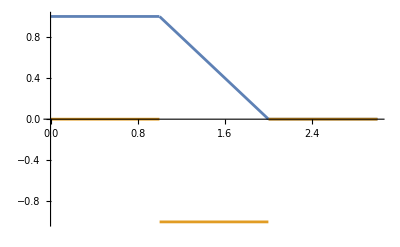

```mathematica
Plot[{polyTrans[x,1,1],Derivative[1,0,0][polyTrans][x,1,1]},{x,0,3}]
```

```mathematica
FullSimplify[polyTrans[x,radius,sigma]]
```

Piecewise[{{1, x<radius}, {0, x>radius+sigma}, {(radius+sigma-x)/sigma, True}}]

## V and p correspondence

We know that the normal vector is a solution to the geodesic equation

```mathematica
geodesicEquations[nU,nL]
```

{0,0,0,0}

How we translate this normal vector to V? We use Vincent equation (8)
Suppose that we have Vx = Vy = Vz = 0

```mathematica
FullSimplify[energy(nU+Join[{0},VU])//.{velx->0,vely->0,velz->0}]
```

{energy,energy ud f[√((-t ub+x)^2+y^2+z^2)],0,0}

Note that this is nU if energy = 1

```mathematica
nU
```

{1,ud f[√((-t ub+x)^2+y^2+z^2)],0,0}

So a particle with Vx = Vy = Vz = 0 and E = 1 follows a geodesic trajectory.
Under these conditions, dE/dt = 0

```mathematica
dEdt//.{velx->0,vely->0,velz->0}
```

0

## Providing an Initial Velocity to the Particles

We now know that choosing Vx = Vy = Vz = 0 and E = 1 is equivalent to choosing a particle with 4-momentum nU
We also know that a curve q^μ(λ) with tangent vector nU satisfies the geodesic equation (and thus is a geodesic)

```mathematica
{t'[λ],x'[λ],y'[λ],z'[λ]}==nU
```

{t'[λ],x'[λ],y'[λ],z'[λ]}=={1,ud f[√((-t ub+x)^2+y^2+z^2)],0,0}

What is the 4-momentum of a particle with velocity Vx = ϵ, Vy = Vz = 0 and E such that the 4-vector is normalized?

```mathematica
FullSimplify[(nU+{0,v0,0,0})/Sqrt[1-v0^2]]
```

{1/(√(1-v0^2)),(v0+ud f[√((-t ub+x)^2+y^2+z^2)])/(√(1-v0^2)),0,0}

We can show it is normalized

```mathematica
ClearAll[vecL];
vecU=FullSimplify[(nU+{0,v0,0,0})/Sqrt[1-v0^2]];
Print["Normalized? ",FullSimplify[Sum[gLL[[a,b]]vecU[[a]]vecU[[b]],{a,1,4},{b,1,4}]==-1]]
ClearAll[vecL];
```

Normalized? True

We now specialize our equations to the problem we are interested in solving. In this case, a particle moving along the x-axis.

```mathematica
Specialize[inn_] := FullSimplify[inn /. {velx->Vx[t],vely->0,velz->0,y->0,z->0,energy->1/Sqrt[1-Vx[t]^2]} /. x->x[t]]
```

```mathematica
dXudt1=Specialize[dXudt]
dVUdt1=Specialize[dVUdt]
dEdt1 = Specialize[dEdt]
```

{ud f[√((-t ub+x[t])^2)]+Vx[t],0,0}

{-(ud Vx[t] (-1+Vx[t]^2) (t ub-x[t]) f'[√((-t ub+x[t])^2)])/(√((-t ub+x[t])^2)),0,0}

(ud Vx[t]^2 (t ub-x[t]) f'[√((-t ub+x[t])^2)])/(√(1-Vx[t]^2) √((-t ub+x[t])^2))

From dXudt, we can see that if we choose y[0]=z[0]=0, we never deviate from the x line and get

If we solve the ODE for a time domain where x>=ut,t<=x/u
This means that

```mathematica
part1=FullSimplify[dXudt1 ,{x[t]>=ub*t}][[1]]
part2=FullSimplify[dVUdt1,{x[t]>=ub*t}][[1]]
part3=FullSimplify[dEdt1 ,{x[t]>=ub*t}]
```

ud f[-t ub+x[t]]+Vx[t]

ud Vx[t] (-1+Vx[t]^2) f'[-t ub+x[t]]

-(ud Vx[t]^2 f'[-t ub+x[t]])/(√(1-Vx[t]^2))

We solve in 3 parts:

Start on the right with x[0]=radius+sigma+δ, Vx[0] = v0

```mathematica
Clear[mkFunction];
mkFunction[newsym_, sym_[arg_]->expr_] := Module[{tmparg},
Print["Making function: ",newsym[arg]," = ",expr];
newsym[tmparg_] := expr /. arg->tmparg;
];
```

```mathematica
ClearAll[f,v0,x,Vx,xf,vf];
f[x_]:=0;
ClearAll[eqs];
eqs=FullSimplify[{x'[t]==part1,Vx'[t]==part2,x[0]==radius+sigma+δ,Vx[0]==v0}];
sol1=DSolve[eqs,{x[t],Vx[t]},t]//FullSimplify;
Print[sol1];
mkFunction[xf,sol1[[1]][[1]]];
mkFunction[vf,sol1[[1]][[2]]];
ClearAll[f];
ClearAll[eqs];
```

{{Vx[t]→v0,x[t]→radius+sigma+t v0+δ}}

Making function: xf[t] = v0

Making function: vf[t] = radius+sigma+t v0+δ

When does it reach the outer radius? Remember, the bubble moves. At a given time, its position is u*t, so the outer radius is at u*t+radius+sigma

```mathematica
Solve[xf[t]==(ub*t+radius+sigma),t]//FullSimplify
```

{{t→-(radius+sigma-v0)/ub}}

It reaches there with speed v0
Now, it is in the middle. It starts off with speed v0 at x[0]==radius+sigma

```mathematica
conds = {x[t]>ub t+radius, x[t]< ub t + sigma + radius,sigma>0, radius>0};
part1=FullSimplify[dXudt1,{conds}][[1]]
part2=FullSimplify[dVUdt1,{conds}][[1]]
part3=FullSimplify[dEdt1,{conds}]
```

ud f[-t ub+x[t]]+Vx[t]

ud Vx[t] (-1+Vx[t]^2) f'[-t ub+x[t]]

-(ud Vx[t]^2 f'[-t ub+x[t]])/(√(1-Vx[t]^2))

```mathematica
ClearAll[f, dsol];
f[x_]:=(radius+sigma-x)/sigma;
ClearAll[eqs];
eqs=FullSimplify[{x'[t]==part1,Vx'[t]==part2,x[0]==radius+sigma,Vx[0]==v0}];
dsol=DSolve[eqs,{x[t],Vx[t]},t]//FullSimplify

ClearAll[f];
ClearAll[eqs];
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is Log[ⅇ^1]-Log[-√(-1+Solve`DirInf[])] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 2 Log[ⅇ^1]-Log[-1+Solve`DirInf[]] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is Log[ⅇ^1]-Log[-√(-1+Solve`DirInf[])] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vx[t]→-ⅇ^((t ud)/sigma)/(√(-1+ⅇ^((2 t ud)/sigma)+1/v0^2)),x[t]→(ⅇ^(-(t ud)/sigma) (ⅇ^((t ud)/sigma) (-sigma ub+(radius+sigma+t ub) ud) v0-sigma √(-1+ⅇ^((2 t ud)/sigma)+1/v0^2) v0+sigma (-1+ub v0)))/(ud v0)},{Vx[t]→ⅇ^((t ud)/sigma)/(√(-1+ⅇ^((2 t ud)/sigma)+1/v0^2)),x[t]→(ⅇ^(-(t ud)/sigma) (ⅇ^((t ud)/sigma) (-sigma ub+(radius+sigma+t ub) ud) v0+sigma √(-1+ⅇ^((2 t ud)/sigma)+1/v0^2) v0+sigma (-1+ub v0)))/(ud v0)}}

Let us now consider the possibility that v0 is positive. To begin our analysis, we plot a test function using solution 2 above.

Making function: xfunc[t] = 200. ⅇ^(-t/8) (-3.98+0.04 √(9999.+ⅇ^(t/4))+0.01 ⅇ^(t/8) (-2+1/2 (8+t/2)))

Making function: vfunc[t] = ⅇ^(t/8)/(√(9999.+ⅇ^(t/4)))

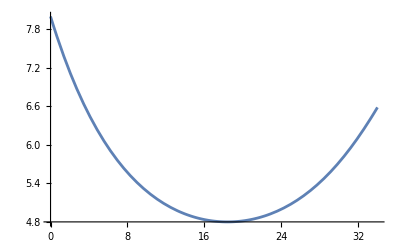

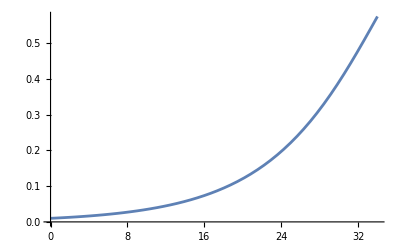

```mathematica
(* pick some parameters *)
Clear[u];
vals= {ub->1/2,ud->1/2,sigma->4,radius->4,v0->.01};
Clear[xfunc,vfunc];
sn=2;
mkFunction[xfunc,dsol[[sn]][[2]] /. vals];
mkFunction[vfunc,dsol[[sn]][[1]] /. vals];
tfin=34;
Plot[xfunc[t]-t/2,{t,0,tfin}]
Plot[vfunc[t],{t,0,tfin}]
```

In the above plot, we see that (relative to the ship), the particle bounces off the warp bubble and goes back outward.

When does it return to the outer radius?

```mathematica
teqn=FullSimplify[Reduce[(x[t] /. dsol[[sn]])==(ub*t+radius+sigma),t,Reals],{sigma∈Reals,ub∈Reals,ub>0,sigma>0,ub>v0,v0>0}];
tsol=Simplify[Solve[teqn,t],{ub<1,ub>0,ub>v0,v0>0}]
tval = t /. tsol[[2]]
```

{{t→0},{t→(sigma Log[(v0+ub (-2+ub v0))/((-1+ub^2) v0)])/ud},{t→Undefined}}

(sigma Log[(v0+ub (-2+ub v0))/((-1+ub^2) v0)])/ud

At this point, it has velocity...

```mathematica
vfin=FullSimplify[Vx[t] /. dsol[[sn]] /. tsol[[2]]]
```

(v0+ub (-2+ub v0))/((-1+ub^2) v0 √(((1+ub^2-2 ub v0)^2)/((-1+ub^2)^2 v0^2)))

If v0 is small, this has the form...

```mathematica
ser=Simplify[Series[vfin,{v0,0,1}],{v0>0,ub>0,ub<1}]
```

(2 ub)/(1+ub^2)-((-1+ub^2)^2 v0)/((1+ub^2)^2)+O[v0]^2

For a warp ship traveling at u = 1/2 c, this is...

```mathematica
ser /. {ub->1/2} // Normal
```

4/5-(9 v0)/25

Now let us consider the case when v0 < 0. This will correspond to solution 1 above.

```mathematica
x[t] /. dsol[[1]]//Simplify
```

(ⅇ^(-(t ud)/sigma) (ⅇ^((t ud)/sigma) (-sigma ub+(radius+sigma+t ub) ud) v0-sigma √(-1+ⅇ^((2 t ud)/sigma)+1/v0^2) v0+sigma (-1+ub v0)))/(ud v0)

```mathematica
FullSimplify[teqn,{sigma∈Reals,u∈Reals,ub>0,ub < 1, ud>0,ud<1,sigma>0,ub>nv0,nv0>0,sigma>0}]
```

t ud+sigma Log[nv0 (1+ub-ud) (1-ub+ud)]==sigma Log[ud+ub (-1-nv0 ub+nv0 ud)+√((nv0+ub)^2+2 (-1+nv0^2) ub ud-(-1+nv0^2) ud^2)]

```mathematica
$Assumptions = {ub > 0, ub < 1, ud > 0, ud < 1, sigma > 0, radius > 0}
```

{ub>0,ub<1,ud>0,ud<1,sigma>0,radius>0}

```mathematica
sn=1;
teqn=FullSimplify[Reduce[(x[t] /. dsol[[sn]] /. v0->-vn0 )==(ub*t+radius),t,Reals],{sigma∈Reals,u∈Reals,ub>0,ub < 1, ud>0,ud<1,sigma>0,ub>vn0,vn0>0,sigma>0}];
tsol=Solve[teqn,t]
tval = t /. tsol[[1]]
```

{{t→ConditionalExpression[(sigma Log[(ub-ud+ub (ub-ud) vn0-√((ub-ud)^2+2 ub vn0+(1+2 ub ud-ud^2) vn0^2))/((-1+(ub-ud)^2) vn0)])/ud, ]}}

ConditionalExpression[(sigma Log[(ub-ud+ub (ub-ud) vn0-√((ub-ud)^2+2 ub vn0+(1+2 ub ud-ud^2) vn0^2))/((-1+(ub-ud)^2) vn0)])/ud, ]

We now substitute this time back into our equation for Vx to obtain the final velocity. To avoid imaginary numbers, we replace v0 with -vn0, a quantity which is positive, and do a Taylor series for small vn0. Because Mathematica seems to have trouble with the case ub==ud, we replace ud with ub+δ and expand in δ. Really, though, we shouldn’t have to worry about small δ.

```mathematica
vfin=FullSimplify[Vx[t] /. dsol[[1]] /. tsol[[1]] /.v0->-vn0 /. ud->ub+δ,{vn0>0,ud>0,ub>0,δ>0,δ<ub}]
```

(δ+ub vn0 δ+√(δ^2+vn0 (vn0+ub (2+ub vn0)-vn0 δ^2)))/(vn0 (-1+δ^2) √(-1+1/vn0^2+((δ+ub vn0 δ+√(δ^2+vn0 (vn0+ub (2+ub vn0)-vn0 δ^2)))^2)/(vn0^2 (-1+δ^2)^2)))

```mathematica
delser=FullSimplify[Series[vfin,{δ,0,2}],{vn0>0}]
```

-(√(vn0 (vn0+ub (2+ub vn0))))/(1+ub vn0)+((1-vn0^2) δ)/(1+ub vn0)^2-(((-1+vn0^2) (-1+2 ub vn0+(2+ub^2) vn0^2)) δ^2)/(2 ((1+ub vn0)^3 √(vn0 (vn0+ub (2+ub vn0)))))+O[δ]^3

```mathematica
ser=Simplify[Series[delser ,{vn0,0,1}],{vn0>0,ub>0,ud>0,ub>ud,δ>0, δ<1}]
```

(-√2 √ub √vn0+O[vn0]^(3/2))+(1-2 ub vn0+O[vn0]^2) δ+(-1/(2 (√2 √ub) √vn0)+((1+21 ub^2) √vn0)/(8 √2 ub^(3/2))+O[vn0]^(3/2)) δ^2+O[δ]^3